```mathematica
(*Force Function*)
f = Compile[{{x, _Real}, {y, _Real},{k, _Real} },{-2.*k*x+k*y,k*x-2*k*y}];
(*Numerically Legendre transform a cumulant generating function into a*rate function*)
RateFunction[cgf_]:=Module[
{lt,slope},
lt=Table[
slope=(cgf[[i+1]][[2]]-cgf[[i-1]][[2]])/(cgf[[i+1]][[1]]-cgf[[i-1]][[1]]);
{-slope,cgf[[i]][[1]] slope-cgf[[i]][[2]]},
{i,2,Length[cgf]-1}];
lt
];

(*Get the Rate Matrix*)
k =1.;
<<MaTeX`
AllNeighbors = Compile[{{i, _Integer}, {sqrtlenfpoints, _Integer}},
(* First handle the four corners *)
If[i==1, {2, sqrtlenfpoints+1},
If[i==sqrtlenfpoints, {sqrtlenfpoints - 1, 2 sqrtlenfpoints},
If[i==sqrtlenfpoints^2-sqrtlenfpoints+1, {sqrtlenfpoints^2-2sqrtlenfpoints+1, sqrtlenfpoints^2-sqrtlenfpoints+2},
If[i==sqrtlenfpoints^2, {sqrtlenfpoints^2-1, sqrtlenfpoints^2-sqrtlenfpoints},
(* Then handle the top and bottom boundary *)
If[1<i<sqrtlenfpoints, {i-1, i+1, i+sqrtlenfpoints},
If[sqrtlenfpoints^2-sqrtlenfpoints+1<i<sqrtlenfpoints^2,{i-1, i+1, i-sqrtlenfpoints},
(* Then handle the left and right boundary *)
If[Mod[i,sqrtlenfpoints]==1, {i-sqrtlenfpoints, i+1, i+sqrtlenfpoints},
If[Mod[i, sqrtlenfpoints]==0, {i-sqrtlenfpoints, i-1, i+sqrtlenfpoints},
(* Otherwise you have four neighbors *)
{i-sqrtlenfpoints, i-1, i+1, i+sqrtlenfpoints}
]
]
]
]
]
]
]
]
];

(* Convert x and y coordinate to the index number of the list *)
xytoi = Compile[{{point, _Real, 1}, {fpoints, _Real, 2}},Position[fpoints, point][[1,1]]];

(* Transition rate to the right *)
Wright = Compile[{{x, _Real}, {y, _Real}, {h, _Real}, {Diffusion, _Real}, {k, _Real}},(f[x,y,k][[1]] / (2h)) + (Diffusion / h^2)];
(* Transition rate to the left *)
Wleft = Compile[{{x, _Real}, {y, _Real}, {h, _Real}, {Diffusion, _Real}, {k, _Real}},-(f[x,y,k] [[1]]/ (2h)) + (Diffusion / h^2)];
(* Transition rate up *)
Wup = Compile[{{x, _Real}, {y, _Real}, {h, _Real}, {Diffusion, _Real}, {k, _Real}},(f[x,y,k] [[2]]/ (2h)) + (Diffusion / h^2)];
(* Transition rate down *)
Wdown = Compile[{{x, _Real}, {y, _Real}, {h, _Real}, {Diffusion, _Real}, {k, _Real}},-(f[x,y,k] [[2]]/ (2h)) + (Diffusion / h^2)];

xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
Diffusion = {250.,25.};
h = {100.,40.}/99.;
(* points is the location of the grid points *)
points = N[Table[{x, y}, {x, xmin, xmax, h[[1]]}, {y, ymin, ymax, h[[2]]}]];
(* Rounded and flattened version of points *)
fpoints = Round[Flatten[points, 1],h[[2]]/400000];
xpoints = N[Table[x, {x, xmin, xmax, h[[1]]}]];
ypoints = N[Table[y, {y, ymin, ymax, h[[2]]}]];

(* Print to notebook. Note that <> is a string concatenation. *)
Print["h = "<>ToString[h]];
Print["Computing edges"];
time = Timing[
(* edges is a list of pairs of vertex numbers that are connected by an edge *)
edges =Flatten[Table[{i, j}, {i,1,Length[fpoints]}, {j, AllNeighbors[i, Sqrt[Length[fpoints]]]}],1];
(*edges =Flatten[Table[{i, xytoi[point1, fpoints]}, {i,1,Length[fpoints]}, {point1, AllNeighbors[fpoints[[i]], fpoints, h]}],1];*)
][[1]];
Print["Computed edges in "<>ToString[time]<>" seconds"];

Print["Constructing Rate Matrix"];
time = Timing[
W = SparseArray[
Table[
(* i and j are indices of the vertices -- they are integers *)
{i,j}=edge;
(* point 1 and point2 are the coordinates of those indices -- they aren't integers *)
point1 = fpoints[[j]];
point2 = fpoints[[i]];
(* This sets the W[[i, j]] matrix element, which is the rate from index j to index i *)
{i,j}->If[point1 - point2 == {0, h[[2]]},Wdown[point1[[1]], point1[[2]], h[[2]], Diffusion[[2]], k], 
If[point1 - point2 == {0, -h[[2]]},Wup[point1[[1]], point1[[2]], h[[2]], Diffusion[[2]], k],If[point1 - point2 == {h[[1]], 0}, 
Wleft[point1[[1]], point1[[2]], h[[1]], Diffusion[[1]], k],
Wright[point1[[1]], point1[[2]], h[[1]], Diffusion[[1]],k]]]],
{edge, edges}
]
];
tot = Total[W, {1}];
Wdiag = Table[
{i, i}->tot[[i]],
{i, 1,Length[fpoints]}
];
W -=SparseArray[Wdiag];

][[1]];
Print["Rate matrix computed in "<>ToString[time] <>" seconds"];
```

h = {1.0101, 0.40404}

Computing edges

Computed edges in 0.040163 seconds

Constructing Rate Matrix

Rate matrix computed in 0.384915 seconds

```mathematica
Print["Computing the top right eigenvector to serve as a seed"];
time = Timing[

evseed = Eigenvectors[W, 1, Method->{"Arnoldi", "Criteria"->"RealPart", "MaxIterations"->250000}][[1]];
][[1]];
Print["Computed the top right eigenvector in "<>ToString[time]<>" seconds"];

time = Timing[
Print[First[
Eigenvalues[N[W],
1,
Method->{"Arnoldi", "Criteria"->"RealPart", "StartingVector"->evseed,"MaxIterations"->250000}
]
]
];
][[1]];
Print["The seeded eigenvalue calculation takes "<>ToString[time]<>" seconds"];

time = Timing[

(* This part is not really necessary because the graph is already fully connected *)
vertexdegrees = VertexDegree[AdjacencyGraph[HeavisideTheta[Sign[W]-0.5]]];keepindices =Reap[Do[If[vertexdegrees[[i]]!= 0, Sow[i]], {i, 1, Length[vertexdegrees]}]][[2]][[1]];W= W[[keepindices, keepindices]];

ev = evseed;
lev = Table[1, {i, 1, Length[W]}];
lev = lev *Length[lev]/ Total[lev];
(* ev is the vector of steady state probabilities *)
ev = Re[evseed / (lev.evseed)];
][[1]];
Print["Computed the top left eigenvector in "<>ToString[time]<>" seconds"];
```

Computing the top right eigenvector to serve as a seed

Computed the top right eigenvector in 10.2063 seconds

-4.04181×10^-14

The seeded eigenvalue calculation takes 0.129766 seconds

Computed the top left eigenvector in 0.21545 seconds

```mathematica
rep=3;
dvec = SparseArray[
Reap[
Do[
{i, j} = edge;Sow[{j,i}->RandomReal[{-1,1}]];,{edge, edges}
]
][[2,1]]
];
sqrtpts = Sqrt[Length[fpoints]];
sqrtplaquettes = sqrtpts - 1;

plaquettes =Table[{i, i}, {i,1,sqrtplaquettes*sqrtplaquettes}];

plaquetteedges = Flatten[Table[{i, j}, {i,1,sqrtplaquettes*sqrtplaquettes}, {j, Join[AllNeighbors[i, sqrtplaquettes], {i}]}], 1];

plaquettedvec = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

llvertex = (t[[1,1]]-1)*sqrtpts + t[[1,2]]; (* vertex number for the lower left vertex of the plaquette *)
xdvec = (dvec[[llvertex, llvertex+sqrtpts]] + dvec[[llvertex +1, llvertex+sqrtpts+1]])/2;
ydvec = (dvec[[llvertex, llvertex+1]] + dvec[[llvertex + sqrtpts, llvertex+sqrtpts+1]])/2 ;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);
{{xcoord, ycoord},{xdvec, ydvec}/h},
{pedge, plaquettes}
];
cmapdvec = (Blend[{RGBColor[{255, 245, 235}/255], RGBColor[{204,76,2}/255]},#]&);
minc= Min[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];
maxc =Max[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];

ticklocationsc = N[FindDivisions[{minc, maxc}, 5]];

minc = ticklocationsc[[1]];
maxc = ticklocationsc[[-1]];
stepc = (maxc - minc) /10.;
cmapdvec2 = cmapdvec[(#-minc) / (4.*stepc)]&;
```

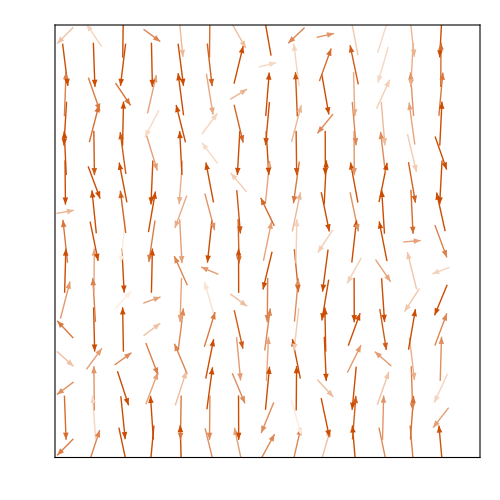

```mathematica
xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
xmajor=25;
xminor=5;
ymajor=5;
yminor=1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,""MaTeX[i, FontSize->16],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->16],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localdvecInitial = Show[
ListVectorPlot[plaquettedvec,
PlotRange->{{xmin, xmax}, {ymin, ymax}},
VectorColorFunction->(cmapdvec2[#5]&),
VectorColorFunctionScaling->False,
VectorScale->{0.04, Automatic, None}
],
Frame->True,
FrameTicks->ft,
FrameLabel->{""MaTeX["x_1",FontSize->16],MaTeX["x_2",FontSize->16]},
ImageSize->500,
AspectRatio->1,
ImagePadding->{{60, 10}, {50, 10}}
]
```

```mathematica
Export["/Users/junangli/Desktop/RandomnewdvectorIni_"<>ToString[rep]<>".mtx",dvec];
```

```mathematica
Clear[z];
Wtilt = W * Exp[z dvec];
ψ=Table[
z = zv;
{eigenval, eigenvec} = 
Chop[
Eigensystem[Wtilt,
1,
Method->{"Arnoldi", "Criteria"->"RealPart", "StartingVector"->evseed,"MaxIterations"->250000}
]
];
{z, First[eigenval]},
{zv, 0.001, 0.002, 0.001}
];
minxval = -ψ[[1,2]] / ψ[[1, 1]];
varval = 4(ψ[[2, 2]] - (ψ[[1,2]] / ψ[[1, 1]])*ψ[[2, 1]]) / (ψ[[2, 1]]^2);
Σold = 2 * (minxval)^2/varval
```

0.0188968

```mathematica
(* Compute scaled cumulant generating function for d = thermodynamic force *)
Clear[z];
Wtilt = W * Exp[z dvec];
ψ=Table[
z = zv;
{eigenval, eigenvec} = 
Chop[
Eigensystem[Wtilt,
1,
Method->{"Arnoldi", "Criteria"->"RealPart", "StartingVector"->evseed,"MaxIterations"->250000}
]
];
{z, First[eigenval]},
{zv, 0.001, 0.002, 0.001}
];
minxval = -ψ[[1,2]] / ψ[[1, 1]];
varval = 4(ψ[[2, 2]] - (ψ[[1,2]] / ψ[[1, 1]])*ψ[[2, 1]]) / (ψ[[2, 1]]^2);
Σold = 2 * (minxval)^2/varval;

dynamicplot = {};
Dynamic[dynamicplot]

acceptances = 0;
trials = 10;
repeatedtrials = 50;
dvec = dvec / minxval;
β = 5000; (* Bigger β prefers the optimal d *)
ΣEstimateValues = {};
Do[
NewΣEstimateValues = Table[
(* Perturb the dvector *)
randamp1 = RandomReal[{-0.5, 0.5}];
randamp2 = RandomReal[{-0.5, 0.5}];
randx = RandomReal[{xmin, xmax}];
randy = RandomReal[{ymin, ymax}];

newdvec = SparseArray[
Reap[
Do[
{i, j} = edge;
Sow[{i,j}->(dvec[[i, j]]+If[i>j, 1, -1]*If[Abs[i-j]==1,(randamp1 Exp[(- Norm[(fpoints[[i,1]]+fpoints[[j,1]])/2 - randx]^2)/(2((xmax-xmin)/10)^2)]Exp[(- Norm[(fpoints[[i,2]]+fpoints[[j,2]])/2 - randy]^2)/(2((ymax-ymin)/10)^2)]-randamp1 Exp[(- Norm[(fpoints[[i,1]]+fpoints[[j,1]])/2 + randx]^2)/(2((xmax-xmin)/10)^2)]Exp[(- Norm[(fpoints[[i,2]]+fpoints[[j,2]])/2 + randy]^2)/(2((ymax-ymin)/10)^2)]), (randamp2 Exp[(- Norm[(fpoints[[i,1]]+fpoints[[j,1]])/2 + randx]^2)/(2((xmax-xmin)/10)^2)]Exp[(- Norm[(fpoints[[i,2]]+fpoints[[j,2]])/2 + randy]^2)/(2((ymax-ymin)/10)^2)]-randamp2 Exp[(- Norm[(fpoints[[i,1]]+fpoints[[j,1]])/2 + randx]^2)/(2((xmax-xmin)/10)^2)]Exp[(- Norm[(fpoints[[i,2]]+fpoints[[j,2]])/2 + randy]^2)/(2((ymax-ymin)/10)^2)])])
];,{edge, edges}
]
][[2,1]]
];

(*If[
rep==300
,Export["/Users/junangli/Desktop/newdvector"<>ToString[rep]<>".mtx",newdvec]
];*)

(* Compute scaled cumulant generating function *)
Clear[z];
Wtilt = W * Exp[z newdvec];

ψ=Table[
z = zv;
{eigenval, eigenvec} = 
Chop[
Eigensystem[Wtilt,
1,
Method->{"Arnoldi", "Criteria"->"RealPart", "StartingVector"->evseed,"MaxIterations"->250000}
]
];
{z, First[eigenval]},
{zv, 0.001, 0.002, 0.001}
];
minxval = -ψ[[1,2]] / ψ[[1, 1]];
varval = 4(ψ[[2, 2]] - (ψ[[1,2]] / ψ[[1, 1]])*ψ[[2, 1]]) / (ψ[[2, 1]]^2);
Σ = 2 * (minxval)^2/varval;

Δenergy =β (Σold - Σ);
If[RandomReal[] <Exp[-Δenergy], 
dvec = newdvec/minxval; acceptances+=1;Σold = Σ
];
 Σold,
{trialNumber, 1, trials}
];
ΣEstimateValues  = Join[ΣEstimateValues , NewΣEstimateValues ];
dynamicplot =ListPlot[ΣEstimateValues],
{repeatedTrialNumber, 1, repeatedtrials}
]
```

```mathematica
Export["/Users/junangli/Desktop/RandomnewdvectorEnd_"<>ToString[rep]<>".mtx",dvec];
Export["/Users/junangli/Desktop/RandomΣEstimateValues_"<>ToString[rep]<>".mat",ΣEstimateValues];
```

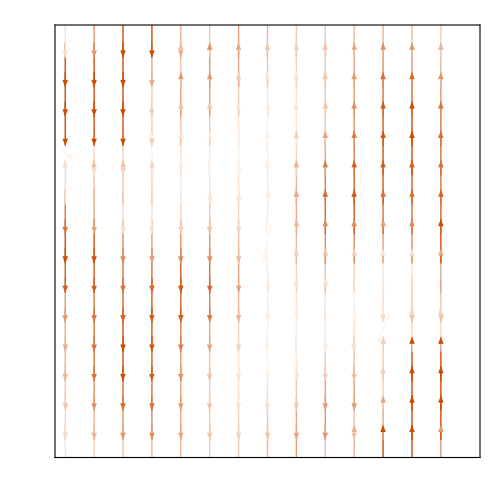

```mathematica
dvec=Import["/Users/junangli/Desktop/RandomnewdvectorEnd_"<>ToString[rep]<>".mtx"];

sqrtpts = Sqrt[Length[fpoints]];
sqrtplaquettes = sqrtpts - 1;

plaquettes =Table[{i, i}, {i,1,sqrtplaquettes*sqrtplaquettes}];
plaquetteedges = Flatten[Table[{i, j}, {i,1,sqrtplaquettes*sqrtplaquettes}, {j, Join[AllNeighbors[i, sqrtplaquettes], {i}]}], 1];

plaquettedvec = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

llvertex = (t[[1,1]]-1)*sqrtpts + t[[1,2]]; (* vertex number for the lower left vertex of the plaquette *)
xdvec = (dvec[[llvertex, llvertex+sqrtpts]] + dvec[[llvertex +1, llvertex+sqrtpts+1]])/2;
ydvec = (dvec[[llvertex, llvertex+1]] + dvec[[llvertex + sqrtpts, llvertex+sqrtpts+1]])/2 ;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);
{{xcoord, ycoord},{xdvec, ydvec}/h},
{pedge, plaquettes}
];

cmapdvec = (Blend[{RGBColor[{255, 245, 235}/255], RGBColor[{204,76,2}/255]},#]&);
minc= Min[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];
maxc =Max[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];

ticklocationsc = N[FindDivisions[{minc, maxc}, 5]];

minc = ticklocationsc[[1]];
maxc = ticklocationsc[[-1]];
stepc = (maxc - minc) /10.;
cmapdvec2 = cmapdvec[(#-minc) / (4.*stepc)]&;

xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
xmajor=25;
xminor=10;
ymajor=10;
yminor=1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,""MaTeX[i, FontSize->16],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->16],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localdvec = Show[
ListVectorPlot[plaquettedvec,
PlotRange->{{xmin, xmax}, {ymin, ymax}},
VectorColorFunction->(cmapdvec2[#5]&),
VectorColorFunctionScaling->False,
VectorScale->{0.04, Automatic, None}
],
Frame->True,
FrameTicks->ft,
FrameLabel->{""MaTeX["x_1",FontSize->16],MaTeX["x_2",FontSize->16]},
ImageSize->500,
AspectRatio->1,
ImagePadding->{{60, 10}, {50, 10}}
]
```